```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
δ=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Mathematica/NP/esperimento/LASER/laser_``.txt",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"λ (nm)"->1,"I"->2|>]&/@{"sample_A","sample_B","sample_C","sample_D","perovskite2"}
```

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

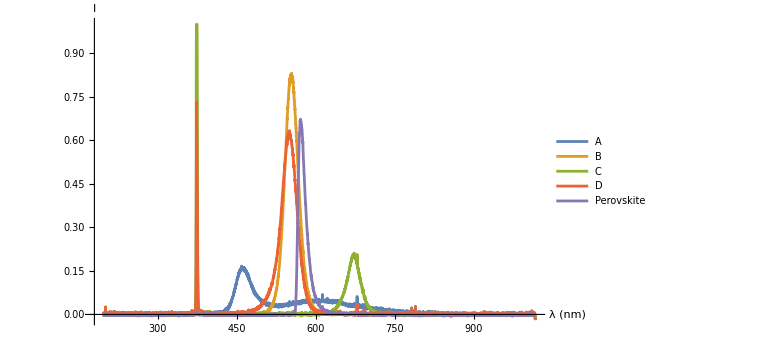

```mathematica
ListLinePlot[Transpose[{#[All,"λ (nm)"],#[All,"I"]}//Normal]&/@δ,PlotRange->All,ImageSize->Large,PlotLegends->{"A","B","C","D","Perovskite"},AxesLabel->{"λ (nm)","I"}]
```